f=1 sol={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}freq={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

f=4 sol={4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80}freq={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

f=2 sol={2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40}freq={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

f=5 sol={5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}freq={5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

f=3 sol={3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60}freq={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

f=6 sol={6,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96,102,108,114,120}freq={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

f=7 sol={7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126,133,140}freq={7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}

f=9 sol={9,18,27,36,45,54,63,72,81,90,99,108,117,126,135,144,153,162,171,180}freq={9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9}

f=8 sol={8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160}freq={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

f=10 sol={10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200}freq={10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

{<|Kf→1,Kres→{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20}}|>,<|Kf→2,Kres→{{2,2},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24},{2,26},{2,28},{2,30},{2,32},{2,34},{2,36},{2,38},{2,40}}|>,<|Kf→3,Kres→{{3,3},{3,6},{3,9},{3,12},{3,15},{3,18},{3,21},{3,24},{3,27},{3,30},{3,33},{3,36},{3,39},{3,42},{3,45},{3,48},{3,51},{3,54},{3,57},{3,60}}|>,<|Kf→4,Kres→{{4,4},{4,8},{4,12},{4,16},{4,20},{4,24},{4,28},{4,32},{4,36},{4,40},{4,44},{4,48},{4,52},{4,56},{4,60},{4,64},{4,68},{4,72},{4,76},{4,80}}|>,<|Kf→5,Kres→{{5,5},{5,10},{5,15},{5,20},{5,25},{5,30},{5,35},{5,40},{5,45},{5,50},{5,55},{5,60},{5,65},{5,70},{5,75},{5,80},{5,85},{5,90},{5,95},{5,100}}|>,<|Kf→6,Kres→{{6,6},{6,12},{6,18},{6,24},{6,30},{6,36},{6,42},{6,48},{6,54},{6,60},{6,66},{6,72},{6,78},{6,84},{6,90},{6,96},{6,102},{6,108},{6,114},{6,120}}|>,<|Kf→7,Kres→{{7,7},{7,14},{7,21},{7,28},{7,35},{7,42},{7,49},{7,56},{7,63},{7,70},{7,77},{7,84},{7,91},{7,98},{7,105},{7,112},{7,119},{7,126},{7,133},{7,140}}|>,<|Kf→8,Kres→{{8,8},{8,16},{8,24},{8,32},{8,40},{8,48},{8,56},{8,64},{8,72},{8,80},{8,88},{8,96},{8,104},{8,112},{8,120},{8,128},{8,136},{8,144},{8,152},{8,160}}|>,<|Kf→9,Kres→{{9,9},{9,18},{9,27},{9,36},{9,45},{9,54},{9,63},{9,72},{9,81},{9,90},{9,99},{9,108},{9,117},{9,126},{9,135},{9,144},{9,153},{9,162},{9,171},{9,180}}|>,<|Kf→10,Kres→{{10,10},{10,20},{10,30},{10,40},{10,50},{10,60},{10,70},{10,80},{10,90},{10,100},{10,110},{10,120},{10,130},{10,140},{10,150},{10,160},{10,170},{10,180},{10,190},{10,200}}|>}

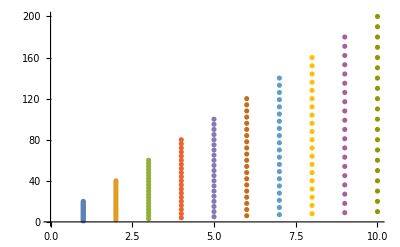

test.txt

```mathematica
fun[f_]:=Block[{aloc,b,t,sol},freq=Table[f,{i,20}];t=Table[i,{i,20}];sol=f*t;Print["f=",f," sol=",sol,"freq=",freq];Association[{Kf-> f,Kres-> Transpose[{freq,sol}]}]
]
(*Association[{Kf-> f,Kt->t,Kres-> sol}]*)

mo=ParallelTable[fun[f],{f,1,10}]
ListPlot[Table[mo[[i]][Kres],{i,10}]]
(*m2=ParallelTable[{i,(1/Rb0)*(Rb[i][1.0*tact+j/i]/.ndsmod)},{j,1.0numperiodsinit,1.0numperiodsfin},{i,1.0freq1*fconf,1.0freq2*fconf,1.0stepfreq*fconf}];//AbsoluteTiming*)

Export["test.txt",mo]
```

```mathematica
data1=Import["test.txt","Table"];


data1[[1]]
```

{<|Kf,->,1,,Kres,->,{{1,,1},,{1,,2},,{1,,3},,{1,,4},,{1,,5},,{1,,6},,{1,,7},,{1,,8},,{1,,9},,{1,,10},,{1,,11},,{1,,12},,{1,,13},,{1,,14},,{1,,15},,{1,,16},,{1,,17},,{1,,18},,{1,,19},,{1,,20}}|>}

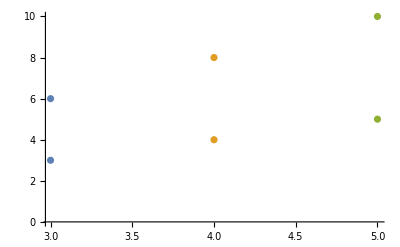

```mathematica
ListPlot[mo]
```

```mathematica
{data1}
```

{{{3, 3}, {3, 6}},
{{4, 4}, {4, 8}},
{{5, 5}, {5, 10}}}

```mathematica
mo
```

{{{3,3},{3,6}},{{4,4},{4,8}},{{5,5},{5,10}}}

```mathematica
{data1}
```

{{{3, 3}, {3, 6}},{{4, 4}, {4, 8}},{{5, 5}, {5, 10}}}

```mathematica
mo - {data1}
```

Thread::tdlen: Objects of unequal length in {{{3,3},{3,6}},{{4,4},{4,8}},{{5,5},{5,10}}}+{-{{3, 3}, {3, 6}},{{4, 4}, {4, 8}},{{5, 5}, {5, 10}}} cannot be combined.

{-{{3, 3}, {3, 6}},{{4, 4}, {4, 8}},{{5, 5}, {5, 10}}}+{{{3,3},{3,6}},{{4,4},{4,8}},{{5,5},{5,10}}}

```mathematica
ListPlot[{{1,{1,2,3}},{2,{5,6,3}},{3,{1,2,4}}}]
```

-Graphics-

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}